```mathematica
(** Data import **)
SetDirectory[NotebookDirectory[]];
```

```mathematica
NamData0=Import["0_11h38min__LCPA.txt","Table"];
NamData15=Import["15_12h12min__LCPA.txt","Table"];
NamData30=Import["30_12h47min__LCPA.txt","Table"];
NamData45=Import["45_11h41min__LCPA.txt","Table"];
S1HN0=Table[NamData0[[n,2]],{n,2,Dimensions[NamData0][[1]]-1,2}];
S2HN0=Table[NamData0[[n,3]],{n,2,Dimensions[NamData0][[1]]-1,2}];
S3HN0=Table[NamData0[[n,4]],{n,2,Dimensions[NamData0][[1]]-1,2}];
S1HN15=Table[NamData15[[n,2]],{n,2,Dimensions[NamData15][[1]]-1,2}];
S2HN15=Table[NamData15[[n,3]],{n,2,Dimensions[NamData15][[1]]-1,2}];
S3HN15=Table[NamData15[[n,4]],{n,2,Dimensions[NamData15][[1]]-1,2}];
S1HN30=Table[NamData30[[n,2]],{n,2,Dimensions[NamData30][[1]]-1,2}];
S2HN30=Table[NamData30[[n,3]],{n,2,Dimensions[NamData30][[1]]-1,2}];
S3HN30=Table[NamData30[[n,4]],{n,2,Dimensions[NamData30][[1]]-1,2}];
S1HN45=Table[NamData45[[n,2]],{n,2,Dimensions[NamData45][[1]]-1,2}];
S2HN45=Table[NamData45[[n,3]],{n,2,Dimensions[NamData45][[1]]-1,2}];
S3HN45=Table[NamData45[[n,4]],{n,2,Dimensions[NamData45][[1]]-1,2}];
Naps0=Table[NamData0[[n,14]],{n,1,Dimensions[NamData0][[1]]-1,2}];
Naps15=Table[NamData15[[n,15]],{n,1,Dimensions[NamData15][[1]]-1,2}];
Naps30=Table[NamData30[[n,15]],{n,1,Dimensions[NamData30][[1]]-1,2}];
Naps45=Table[NamData45[[n,13]],{n,1,Dimensions[NamData45][[1]]-1,2}];
step=1;
od=1;
BlochMer0=Table[{S1HN0[[n]],S2HN0[[n]],S3HN0[[n]]},{n,od,Dimensions[S1HN0][[1]],step}];
BlochMer15=Table[{S1HN15[[n]],S2HN15[[n]],S3HN15[[n]]},{n,od,Dimensions[S1HN15][[1]],step}];
BlochMer30=Table[{S1HN30[[n]],S2HN30[[n]],S3HN30[[n]]},{n,od,Dimensions[S1HN30][[1]],step}];
BlochMer45=Table[{S1HN45[[n]],S2HN45[[n]],S3HN45[[n]]},{n,od,Dimensions[S1HN45][[1]],step}];
Naps0a=Table[Naps0[[n]],{n,od,Dimensions[Naps0][[1]],step}];
Naps15a=Table[Naps15[[n]],{n,od,Dimensions[Naps15][[1]],step}];
Naps30a=Table[Naps30[[n]],{n,od,Dimensions[Naps30][[1]],step}];
Naps45a=Table[Naps45[[n]],{n,od,Dimensions[Naps45][[1]],step}];
```

```mathematica
(** Theoretical model **)
```

```mathematica
states={{{1},{0}},{{0},{1}},1/Sqrt[2]*{{1},{1}},1/Sqrt[2]*{{1},{-1}},1/Sqrt[2]*{{1},{I}},1/Sqrt[2]*{{1},{-I}}}; (* All base states *)
stateIn=states[[1]]; (* Input state - pol. output *)
rot[x_]:={{Cos[x],Sin[x]},{-Sin[x],Cos[x]}} (* rot. matrix *)
gamma[u_]:=retfun[u]
X[u_]:=Sqrt[(phi^2)+gamma[u]^2]
```

```mathematica
retfun[u_]:=a+1/(b+Exp[d-c*(u^e)])(* Logistic function *)
```

```mathematica
lcmat[u_]:={{Cos[X[u]]+(ⅈ gamma[u] Sin[X[u]])/X[u],-(phi Sin[X[u]])/X[u]},{(phi Sin[X[u]])/X[u],Cos[X[u]]-(ⅈ gamma[u] Sin[X[u]])/X[u]}}(* Final TNLCc matrix *)
```

```mathematica
total[beta_,u_]:=rot[-beta].rot[phi].lcmat[u].rot[beta] (* Final TNLCc matrix of a rotated TNLCc by betha *)
```

```mathematica
ident={{1,0},{0,1}};
sigma2={{0,1},{1,0}};
sigma3={{0,-I},{I,0}};
sigma2cc={{0,I},{-I,0}};
sigma1={{1,0},{0,-1}};
sigma={sigma1,sigma2,sigma3}; (* Definition of the Sigma matrices *)

bloch[rho_]:=Table[ Re[Tr[sigma[[i]].rho]],{i,1,3}] (* density matrix -> bloch vec. *)
ketOut[beta_,u_]:=total[beta,u].stateIn (* Final output pol.state - ket *)
braOut[beta_,u_]:=ConjugateTranspose[total[beta,u].stateIn] (* Final output pol.state - bra *)
rhoOut[beta_,u_]:=KroneckerProduct[braOut[beta,u],ketOut[beta,u]] (* Final output pol.state - density matrix *)

(** Def. states for fit - rotated TNLCc by angles 4 **)
VysTupTHJ0=ketOut[theta,V];
rhoVysTup0=rhoOut[theta,V];
VysTupTHS0=bloch[rhoVysTup0];

VysTupTHJ15=ketOut[theta+N[11°],V];
rhoVysTup15=rhoOut[theta+N[11°],V];
VysTupTHS15=bloch[rhoVysTup15];

VysTupTHJ30=ketOut[theta+N[26°],V];
rhoVysTup30=rhoOut[theta+N[26°],V];
VysTupTHS30=bloch[rhoVysTup30];

VysTupTHJ45=ketOut[theta+N[41°],V];
rhoVysTup45=rhoOut[theta+N[41°],V];
VysTupTHS45=bloch[rhoVysTup45];

VysTupTHSNap0=Table[VysTupTHS0/.{V->Naps0a[[n]]},{n,1,Dimensions[Naps0a][[1]]}];
VysTupTHSNap15=Table[VysTupTHS15/.{V->Naps15a[[n]]},{n,1,Dimensions[Naps0a][[1]]}];
VysTupTHSNap30=Table[VysTupTHS30/.{V->Naps30a[[n]]},{n,1,Dimensions[Naps0a][[1]]}];
VysTupTHSNap45=Table[VysTupTHS45/.{V->Naps45a[[n]]},{n,1,Dimensions[Naps0a][[1]]}];
```

```mathematica
(** FIT **)
```

```mathematica
SeedRandom[1];
```

```mathematica
initials = {{-8.314031137459752,0.07364228363744871,174.92047651524567,-2.9721437986637023,-2.8536892547196415,-5.145593598118274,-2.56022951974189}};
```

```mathematica
FitPar=NMinimize[{ParallelSum[Sum[(BlochMer0[[m,n]]-VysTupTHSNap0[[m,n]])^2,{n,{1,2,3}}],{m,1,Dimensions[BlochMer0][[1]]}]+ParallelSum[Sum[(BlochMer30[[m,n]]-VysTupTHSNap30[[m,n]])^2,{n,{1,2,3}}],{m,1,Dimensions[BlochMer30][[1]]}]+ParallelSum[Sum[(BlochMer15[[m,n]]-VysTupTHSNap15[[m,n]])^2,{n,{1,2,3}}],{m,1,Dimensions[BlochMer15][[1]]}]+ParallelSum[Sum[(BlochMer45[[m,n]]-VysTupTHSNap45[[m,n]])^2,{n,{1,2,3}}],{m,1,Dimensions[BlochMer45][[1]]}],Min[ParallelSum[retfun[v],{v,0.1,10.1}]]≥0},{a,b,c,d,e,phi,theta},Method->{"Automatic","InitialPoints"->initials},MaxIterations->200(*,StepMonitor:>Print["Step to theta = ",theta]*)]
stop=AbsoluteTime[];
stop-start
```

{10.275,{a→-7.82057,b→0.0761821,c→176.156,d→-2.89523,e→-2.86832,phi→-5.15607,theta→-2.58144}}

4716.075161

```mathematica
(** Export **)
```

```mathematica
FitDATA = {a->-7.820573268569158,b->0.07618212773600479,c->176.1560023971697,d->-2.89522737626486,e->-2.8683220566787044,phi->-5.156073407255145,theta->-2.581437502776475};
VysTupTHS0a=VysTupTHS0/.FitDATA;
VysTupTHS15a=VysTupTHS15/.FitDATA;
VysTupTHS30a=VysTupTHS30/.FitDATA;
VysTupTHS45a=VysTupTHS45/.FitDATA;
Vod=0.01;
Vto=10;
```

```mathematica
Angle1=Pi/8-Pi/20;
Angle2=-Pi/8-Pi/20;
```

```mathematica
ForExport=Show[ListPointPlot3D[BlochMer15,BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},PlotStyle->Directive[PointSize[0.015],Opacity[.5],RGBColor[.7,0,0]],Axes->False,Boxed->False],ListPointPlot3D[BlochMer30,BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},PlotStyle->Directive[PointSize[0.015],Opacity[.5],RGBColor[0,.5,0]],Axes->False,Boxed->False],ListPointPlot3D[BlochMer45,BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},PlotStyle->Directive[PointSize[0.015],Opacity[.5],RGBColor[0,0,.6]],Axes->False,Boxed->False],ParametricPlot3D[VysTupTHS15a,{V,Vod,Vto},PlotStyle->{RGBColor[1,0,0],Thick}],ParametricPlot3D[VysTupTHS30a,{V,Vod,Vto},PlotStyle->{RGBColor[0,1,0],Thick}],ParametricPlot3D[VysTupTHS45a,{V,Vod,Vto},PlotStyle->{RGBColor[0,0,1],Thick}],ParametricPlot3D[{0,Sin[a],Cos[a]},{a,0+Angle1,Pi+Angle1},PlotStyle->{Black,Dashed,Thin}],ParametricPlot3D[{0,Sin[a],Cos[a]},{a,Pi+Angle1,2Pi+Angle1},PlotStyle->{Black,Thin}],ParametricPlot3D[{Sin[a],Cos[a],0},{a,-Pi/2+Angle2,Pi/2+Angle2},PlotStyle->{Black,Dashed,Thin}],ParametricPlot3D[{Sin[a],Cos[a],0},{a,Pi/2+Angle2,3Pi/2+Angle2},PlotStyle->{Black,Thin}],Graphics3D[{{RGBColor[0.5,0.5,0.5,.5],Arrowheads[0.04],Thickness[0.008],Arrow[{{{0,0,0},{1,0,0}},{{0,0,0},{-1,0,0}},{{0,0,0},{0,1,0}},{{0,0,0},{0,-1,0}},{{0,0,0},{0,0,1}},{{0,0,0},{0,0,-1}}}]},{Opacity[.3],Yellow,Sphere[{0,0,0}]}}],Graphics3D[Style[Text["R",{0,0,1.1}],Black,Italic,30]],Graphics3D[Style[Text["L",{0,0,-1.1}],Black,Italic,30]],Graphics3D[Style[Text["D",{0,1.1,0}],Black,Italic,30]],Graphics3D[Style[Text["A",{0,-1.1,0}],Black,Italic,30]],Graphics3D[Style[Text["H",{1.1,0,0}],Black,Italic,30]],Graphics3D[Style[Text["V",{-1.1,0,0}],Black,Italic,30]],Background->Transparent,ImageSize->600]
```

-Graphics3D-

```mathematica
(** Hammer projection **)
GetSpherical[Bloch_]:={ArcTan[Sqrt[Bloch[[2]]^2+Bloch[[1]]^2],Bloch[[3]]],Limit[ArcTan[x,Bloch[[2]]],{x->Bloch[[1]]}]}
```

```mathematica
blochlistStates={{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}};
```

```mathematica
(* Rotate Hammer proj @90deg {0,0,1} *)
```

```mathematica
rotVec = {0,0,1} ;(* Rot. axis *)
angleRot = 3Pi/4(*-Pi/4*);(* Rot. angle *)
```

```mathematica
HammerCoordinates[bloch_]:=ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->GetSpherical[RotationMatrix[angleRot,rotVec].bloch][[1]],az->GetSpherical[RotationMatrix[angleRot,rotVec].bloch][[2]]},{2}]
```

```mathematica
zero = -1*10^(-16); (* correction only for state plotting *)
```

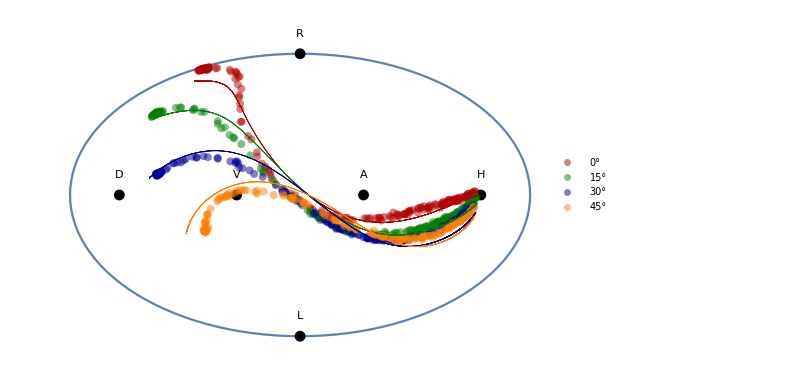

```mathematica
HammerPlot=Show[ListPlot[Table[ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->Range[0.,2*Pi,2*Pi/120][[i]],az->Pi},{2}],{i,1,121}],Joined->{True,False}],ListPlot[Table[HammerCoordinates[blochlistStates[[i]]+{zero,zero,zero}],{i,1,6}],PlotStyle->{PointSize[0.013],RGBColor[0,0,0]}],
ListPlot[Table[HammerCoordinates[BlochMer0[[i]]],{i,1,Dimensions[BlochMer0][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[.7,0,0],Opacity[0.5]},PlotLegends->{"0°"}],
ListPlot[Table[HammerCoordinates[BlochMer15[[i]]],{i,1,Dimensions[BlochMer15][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,.5,0],Opacity[0.5]},PlotLegends->{"15°"}],
ListPlot[Table[HammerCoordinates[BlochMer30[[i]]],{i,1,Dimensions[BlochMer30][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,0,.6],Opacity[0.5]},PlotLegends->{"30°"}],
ListPlot[Table[HammerCoordinates[BlochMer45[[i]]],{i,1,Dimensions[BlochMer45][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[1,.5,0],Opacity[0.5]},PlotLegends->{"45°"}],
ListPlot[ParallelTable[HammerCoordinates[VysTupTHS0a],{V,Vod,Vto,0.001}],PlotStyle->{PointSize[0.00095],RGBColor[.7,0,0],Opacity[0.9]}],
ListPlot[ParallelTable[HammerCoordinates[VysTupTHS15a],{V,Vod,Vto,0.001}],PlotStyle->{PointSize[0.00095],RGBColor[0,.5,0],Opacity[0.9]}],
ListPlot[ParallelTable[HammerCoordinates[VysTupTHS30a],{V,Vod,Vto,0.001}],PlotStyle->{PointSize[0.00095],RGBColor[0,0,0.6],Opacity[0.9]}],
ListPlot[ParallelTable[HammerCoordinates[VysTupTHS45a],{V,Vod,Vto,0.001}],PlotStyle->{PointSize[0.00095],RGBColor[1,.5,0],Opacity[0.9]}],
(*ListPlot[Table[HammerCoordinates[BlochListR[[i]]],{i,1,6}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
ListPlot[Table[HammerCoordinates[BlochListL[[i]]],{i,1,6}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],*)
Graphics[Style[Text["H",HammerCoordinates[{1,zero,zero}]+{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["V",HammerCoordinates[{-1,zero,zero}]+{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["D",HammerCoordinates[{zero,1,zero}]+{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["A",HammerCoordinates[{zero,-1,zero}]+{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["R",HammerCoordinates[{zero,zero,1}]+{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["L",HammerCoordinates[{zero,zero,-1}]+{0,0.2}],Black,Italic,30]],
PlotRange->All,Axes->False,ImageSize->600]
```

```mathematica
Export["Fit_Hammer_ROT.pdf",HammerPlot,ImageResolution->600]
```

Fit_Hammer_ROT.pdf

```mathematica
(** Fidelity - model vs. data **)
Fidelity[u_,v_]:=Re[1/2(1+u.v+Sqrt[(1-Norm[u])(1-Norm[v])]) ]
```

```mathematica
BlochModel0 = ParallelTable[VysTupTHS0a/.V->Naps0a[[i]],{i,1,Dimensions[Naps0a][[1]]}];
BlochModel15 = ParallelTable[VysTupTHS15a/.V->Naps15a[[i]],{i,1,Dimensions[Naps15a][[1]]}];
BlochModel30 = ParallelTable[VysTupTHS30a/.V->Naps30a[[i]],{i,1,Dimensions[Naps30a][[1]]}];
BlochModel45 = ParallelTable[VysTupTHS45a/.V->Naps45a[[i]],{i,1,Dimensions[Naps45a][[1]]}];
```

```mathematica
Fidel0 = ParallelTable[Fidelity[BlochMer0[[i]],BlochModel0[[i]]],{i,1,Dimensions[BlochMer0][[1]]}];
Fidel15 = ParallelTable[Fidelity[BlochMer15[[i]],BlochModel15[[i]]],{i,1,Dimensions[BlochMer15][[1]]}];
Fidel30 = ParallelTable[Fidelity[BlochMer30[[i]],BlochModel30[[i]]],{i,1,Dimensions[BlochMer30][[1]]}];
Fidel45 = ParallelTable[Fidelity[BlochMer45[[i]],BlochModel45[[i]]],{i,1,Dimensions[BlochMer45][[1]]}];
```

```mathematica
Mean[Join[Fidel0,Fidel15,Fidel30,Fidel45]]
```

0.996788

```mathematica
StandardDeviation[Join[Fidel0,Fidel15,Fidel30,Fidel45]]
```

0.00423908

```mathematica
(** Angle - model vs. data **)
Angle[u_,v_]:=1/2*(ArcCos[u.v/(Norm[u]*Norm[v])])
```

```mathematica
Angle0 = ParallelTable[Angle[BlochMer0[[i]],BlochModel0[[i]]],{i,1,Dimensions[BlochMer0][[1]]}];
Angle15 = ParallelTable[Angle[BlochMer15[[i]],BlochModel15[[i]s]],{i,1,Dimensions[BlochMer15][[1]]}];
Angle30 = ParallelTable[Angle[BlochMer30[[i]],BlochModel30[[i]]],{i,1,Dimensions[BlochMer30][[1]]}];
Angle45 = ParallelTable[Angle[BlochMer45[[i]],BlochModel45[[i]]],{i,1,Dimensions[BlochMer45][[1]]}];
```

```mathematica
Mean[Join[Angle0,Angle15,Angle30,Angle45]]/Degree
```

2.7249

```mathematica
StandardDeviation[Join[Angle0,Angle15,Angle30,Angle45]]/Degree
```

1.77509